## Riccati ODE

Het eerste wat we doen is de perturbatieve oplossing definiëren. We beginnen met het definiëren van de rij c_n.

```mathematica
c[n_]:=Piecewise[{{1,0<=n<=2},{c[n-1]+Sum[((n-l-3)! l! (c[n-l-3])! l!)/(n!),{l,0,n-3}],n>=3}}];
```

```mathematica
Table[c[n],{n,0,10}]
```

{1,1,1,7/6,5/4,157/120,41/30+(7/6!)/120,1877/1260+(7/6!)/105+(5/4!)/210,9389/5040+(17 7/6!)/1680+(3 5/4!)/560+(157/120!)/336,3361/1008+(3 7/6!)/280+(17 5/4!)/3024+(5 157/120!)/1512+1/504 (41/30+(7/6!)/120)!,3523/336+(7 7/6!)/600+(443 5/4!)/75600+(13 157/120!)/3780+(11 (41/30+(7/6!)/120)!)/5040+1/720 (1877/1260+(7/6!)/105+(5/4!)/210)!}

```mathematica
f0[z_]:=Sum[(-1)*n!*c[n]*z^(-n-1),{n,0,Infinity}];
f0Approx[z_,maxN_]:= Sum[(-1)*n!*c[n]*z^(-n-1),{n,0,maxN}];
Bf0[t_]:= Sum[(-1)*c[n]* t^n,{n,0,Infinity}];
Bf0Approx[t_,maxN_]:=  Sum[(-1)*c[n]* t^n,{n,0,maxN}];
```

We willen de convergentie van Bf0 testen voor waarden van t op de reële as. Hier gebruiken we enkele functies die we uitleggen:
* Module: Dit creëert een lokale omgeving waarin we de variabele kunnen 		definiëren. Hier is de variabele ‘approx’.
* NumericQ[approx]&&!NumberQ[approx]: Dit stelt als voorwaarde dat 		‘approx’ een numerieke waarde is en dat het geen getal is, dus of het een complex getal of een niet numerieke waarde is.

```mathematica
convergenceTest[t_,maxN_]:=Module[{approx},approx=Bf0Approx[t,maxN];
If[NumericQ[approx]&&!NumberQ[approx],"Divergent","Convergent"]]
```

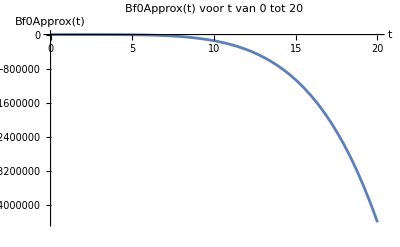

```mathematica
Plot[Bf0Approx[t,50],{t,0,5},PlotRange->All,PlotLabel->"Bf0Approx(t) voor t van 0 tot 20",AxesLabel->{"t","Bf0Approx(t)"}]
```

```mathematica
tValues=Range[0,20,0.1]; (*Kies een interval en stapgrootte*)
BfValues=Bf0Approx[#,20] & /@ tValues ;(*Past Bf0Approx to op alle elementen van tValues*)
```

Vanaf nu werken we verder met f0Approx en Bf0Approx op nauwkeurigheid 20 (maxN=20).